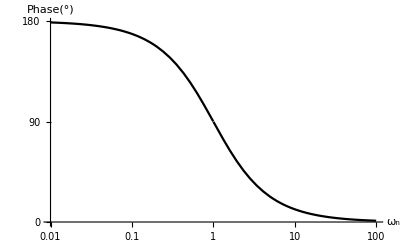

```mathematica
Hap[s_]:=(s-1)/(s+1);
LogLinearPlot[180/π*Arg[Hap[ⅈ ω]],{ω,0.01,100},PlotTheme->"Monochrome",AxesLabel->{"ω_n","Phase(°)"},Ticks->{Automatic,{-180,-135,-90,-45,0,45,90,135,180}}]
```

```mathematica
Simplify[ComplexExpand[Arg[Hap[ⅈ ω]],TargetFunctions->{Re, Im}],Assumptions->ω>0]
```

ArcTan[-1+ω^2,2 ω]

ArcTan[(-ω^2+Q^2 (-1+ω^2)^2)/(ω^2+Q^2 (-1+ω^2)^2),(2 Q ω (-1+ω^2))/(ω^2+Q^2 (-1+ω^2)^2)]

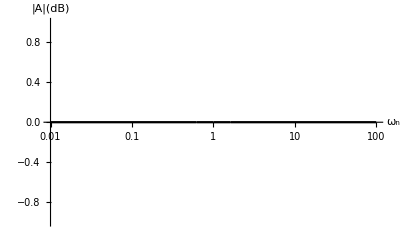

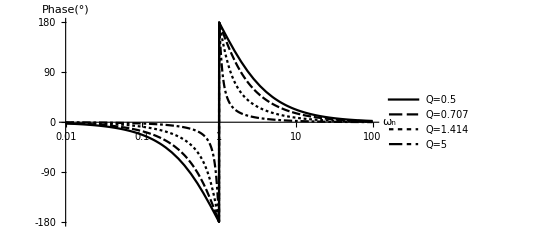

```mathematica
HAP2[s_,Q_]:=(s^2-s/Q+1)/(s^2+s/Q+1);
dB[a_]:=20 Log10[Abs[a]];
deg[a_]:=180/π*Arg[a];
TrigReduce[Simplify[ComplexExpand[Arg[HAP2[ⅈ ω,Q]],TargetFunctions->{Re, Im}]]]
LogLinearPlot[dB[HAP2[ⅈ ω,1]],{ω,0.01,100},PlotTheme->"Monochrome",AxesLabel->{"ω_n","|A|(dB)"},PlotRange->{-1,1}]
LogLinearPlot[{deg[HAP2[ⅈ ω,0.5]],deg[HAP2[ⅈ ω,0.707]],deg[HAP2[ⅈ ω,1.414]],deg[HAP2[ⅈ ω,5]]},{ω,0.01,100},PlotTheme->"Monochrome",AxesLabel->{"ω_n","Phase(°)"},PlotLegends->{"Q=0.5","Q=0.707","Q=1.414","Q=5"},Ticks->{Automatic,{-180,-135,-90,-45,0,45,90,135,180}},PlotRange->{-180,180},Exclusions->None]
```

```mathematica
-Graphics-(*R4->R2,R2->4R2*);
(* R3->R1, R2->4R2, R4->R2 *)
-Graphics-;
sol=Solve[{
(ui-ua)/R1+(uo-ua)/(1/(s C1))+(ub-ua)/(1/(s C1))==0,
(ua-ub)/(1/(s C1))+(uo-ub)/(4 R2)==0,
(ui R2)/(R1+R2)==ub
},{ua,ub,uo}];
uo/.sol[[1]]
```

(R2 (1-2 C1 R1 s+4 C1^2 R1 R2 s^2) ui)/((R1+R2) (1+2 C1 R1 s+4 C1^2 R1 R2 s^2))

```mathematica
(* (s^2-s/Q+1)/(s^2+s/Q+1) *)
Solve[{
4 C1^2 R1 R2 ω^2==1,
2 C1 R1 ω==1/Q
},{R1,R2}]
```

{{R1→1/(2 C1 Q ω),R2→Q/(2 C1 ω)}}

```mathematica
FullSimplify[R2/(R1+R2)/.{R1->1/(2 C1 Q ω),R2->Q/(2 C1 ω)}]
```

Q^2/(1+Q^2)